```mathematica
(*модифицировал программу Дробышева на "Математике" для вычисления запаздывающего скалярно-векторного потенциала по Менде.
Во-первых,последовательными итерациями решается уравнение для нахождения запаздывающего момента времени $t'$:$$c(t-t')=r(t')$$.
Здесь $r(t')=\sqrt{(x-s(t'))^2+y^2}$-расстояние от заряда до точки наблюдения $(x,\,y)$ в момент $t'$,а $s(t)$-текущая координата заряда.
Во-вторых,сама формула для потенциала
cosh(v[t2]*y/(t-t2))/(t-t2)*)
vk=0.84; (* конечная скорость *)
```

```mathematica
a= 0.3; (* ускорение *)
```

```mathematica
epsilon = 10^(-10); (* погрешность *)
```

```mathematica
t0=vk/a; (*время разгона*)
```

```mathematica
s[t_]:=If[t<0,0, If[t<t0, a*t^2/2, vk *t-a * t0^2/2]];(*координата от времени*)
```

```mathematica
v[t_]:=If[t<0, 0, If[t < t0, a *t, vk]]; (*скорость от времени*)
```

```mathematica
phi[x_,y_,t_]:=Module[{t1,t2}, t1=t; t2=t-2* epsilon;(*расчёт итерациями запаздывающего момента t2 *)
While[Abs[t1-t2]>epsilon, t1=t2; t2=t-Sqrt[(x-s[t1])^2+y^2]];(*при расчетах $r$ можно заменить на $c(t-t')$*)
Cosh[v[t2]*y/(t-t2)]/(t-t2)(*скалярно-векторный потенциал по Менде*)
];
```

```mathematica
ss=
Table[Show[ContourPlot[phi[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,0.05,0.95,0.05}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]], {t,0,30,0.25}];
Export["D://scalar-vector-mende-potencial.gif",ss]
```

D://scalar-vector-mende-potencial.gif

```mathematica
t=7.5;
```

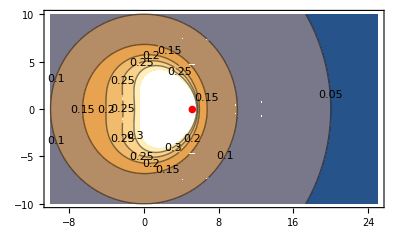

```mathematica
Show[ContourPlot[phi[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,0.05,10.95,0.05}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]]
```

```mathematica
Plot3D[phi[x,y,t],{x,-10,10},{y,-10,10}, {z, -100, 100}]
```

Plot3D::nonopt: Options expected (instead of {z,-100,100}) beyond position 3 in Plot3D[phi[x,y,t],{x,-10,10},{y,-10,10},{z,-100,100}]. An option must be a rule or a list of rules.

Plot3D[phi[x,y,t],{x,-10,10},{y,-10,10},{z,-100,100}]

```mathematica
phi[5,7,t]
```

0.116248